## Taylor Series

For a smooth function f the Taylor polynomial of order n around x_0 
	p_n(x)=∑_(i=0)^n (a_i(x-x_0))^i  with a_i=
is the best polynomial approximation (in the sense that it fits as many derivatives as possible) at x_0.

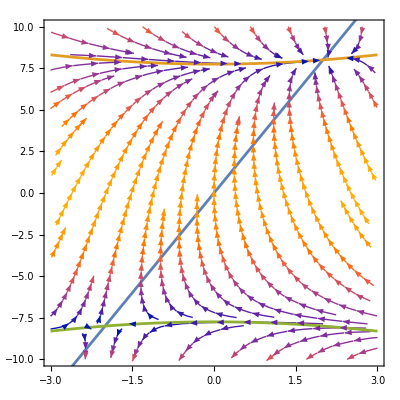

```mathematica
f[{x_,y_}]:= {y-4 x, x^2 - y^2 +60}
Show[
StreamPlot[f[{x,y}],{x,-3,3},{y, -10,10}],
Plot[ {4x , √(x^2+60),-√(x^2+60)},{x, -3,3}]]
```

```mathematica
Eigenvalues[({{-4., 1}, {-4, 16}})]
```

{15.798,-3.79796}

## Pade Approximation

For a smooth function f a Pade approximation of order [m_1/m_2] around x_0 
	r(x)=(p_m_1(x))/(q_m_2(x))  where p_m_1(x)=∑_(i=0)^m_1 (b_i(x-x_0))^i and q_m_2(x)=∑_(i=0)^m_2 (c_i(x-x_0))^i
is a best rational approximation (in the sense that it fits as many derivatives as possible) at x_0.  It is common to normalize with either
	∑_(i=0)^m |c_i|^2=1  or c_0=1.

## Pade vs Taylor

The approximation behavior is quite different.   The Taylor polynomial diverges at the nearest singularity. The Pade approximation can go approximate and sort-of go round a singularity.

```mathematica
f[x_]:=(3.0+Sin[x]+Cos[x])/(x^2+1)
n=5;{m1,m2}={3,2};
p[x_]=Normal[Series[f[x],{x,0,n}]];
r[x_]=PadeApproximant[f[x],{x,0,{m1,m2}}]
TabView[{
"Fun & Tay & Pade"->Plot[{f[x],p[x],r[x]},{x,-1,1}],
"|Fun-Tay| & |Fun-Pade|"->LogPlot[{Abs[f[x]-p[x]],Abs[f[x]-r[x]]},{x,-1,1}],
"log-log"->LogLogPlot[{x^6,Abs[f[x]-p[x]],Abs[f[x]-r[x]]},{x,0,1}]
}]
TabView[{
"Fun"->ComplexPlot3D[f[z],{z,1.5}],
"Tay"->ComplexPlot3D[p[z],{z,1.5}],
"Pade"->ComplexPlot3D[r[z],{z,1.5}],
"Fun-Pade"->ComplexPlot3D[f[z]-r[z],{z,1.5}]
}]
```

(4.+1.00204 x-0.462982 x^2-0.159833 x^3)/(1.+0.000509716 x+1.00913 x^2)

123

1234

Not all singularities are the same!  Square roots have branch-cuts.

```mathematica
f[x_]:=(3.0+Sin[x]+Cos[x])/(√(x^2+1))
n=5;{m1,m2}={3,2};
p[x_]=Normal[Series[f[x],{x,0,n}]];
r[x_]=PadeApproximant[f[x],{x,0,{m1,m2}}]
TabView[{
"Fun & Tay & Pade"->Plot[{f[x],p[x],r[x]},{x,-1,1}],
"|Fun-Tay| & |Fun-Pade|"->LogPlot[{Abs[f[x]-p[x]],Abs[f[x]-r[x]]},{x,-1,1}],
"log-log"->LogLogPlot[{x^6,Abs[f[x]-p[x]],Abs[f[x]-r[x]]},{x,0,1}]
}]
TabView[{
"Fun"->ComplexPlot3D[f[z],{z,1.5},PlotRange->{0,8}],
"Tay"->ComplexPlot3D[p[z],{z,1.5},PlotRange->{0,8}],
"Pade"->ComplexPlot3D[r[z],{z,1.5},PlotRange->{0,8}],
"Fun-Pade"->ComplexPlot3D[f[z]-r[z],{z,1.5},PlotRange->{0,8}]
}]
```

(4.+1.02257 x+0.366291 x^2+0.0343912 x^3)/(1+0.00564175 x+0.715162 x^2)

123

1234

Not surprisingly in our homotopy problems we generically have square root singularities!

## Pade ⟷ Taylor

You can convert between from a Taylor series to a Pade approximant.

```mathematica
PadeApproximant[ Sum[Subscript[a, i] t^i,{i,0,6}],{t,0,{2,2}}]
```

(a_0+(t (-a_1 a_2^2+a_1^2 a_3+a_0 a_2 a_3-a_0 a_1 a_4))/(-a_2^2+a_1 a_3)+(t^2 (a_2^3-2 a_1 a_2 a_3+a_0 a_3^2+a_1^2 a_4-a_0 a_2 a_4))/(a_2^2-a_1 a_3))/(1+(t (-a_2 a_3+a_1 a_4))/(a_2^2-a_1 a_3)+(t^2 (-a_3^2+a_2 a_4))/(-a_2^2+a_1 a_3))

We are going learn how to do this using linear algebra.  Centering at z_0=0 we want
	f(z)=∑_(i=0)^∞ f_i z^i~(∑_(j=0)^m_1 b_j z^j)/(∑_(k=0)^m_2 c_k z^k).
We want to choose the m_1+1 coefficients b_(0:m_1) and the 1+m_2 coefficients c_(0:m_2) to match as many terms of the Taylor series as possible.  Accounting for the normalization of the c coefficients we can hope to match n=m_1+1+m_2+1-1 coefficients. We want
	 ∑_(i=0)^n a_i z^i+O(z^(n+1))~(∑_(j=0)^m_1 b_j z^j)/(∑_(k=0)^m_2 c_k z^k)
If we clear the fraction we get
	∑_(i=0)^n a_i z^i(∑_(k=0)^m_2 c_k z^k)+O(z^(n+1))=∑_(j=0)^m_1 b_j z^j.
There are n+1 equations here one for each power z^0,z^1,(…z)^m_1,…,z^n.  The n+1 coefficients a_0,a_1,…,a_n are known.  We want to compute the m_1+m_2 unknowns b_(0:m_1)and c_(1:m_2).   Notice that powers z^(m_1+1) and above do not involve b_(0:m_1)at all.

This is actually just linear algebra!  We need to choose c_(0:m_2)in the null space of a specific matrix and normalize it and then compute b_(0:m_2) by doing a matrix multiplication.   To see this look a the pattern in the coefficients of
	∑_(i=0)^n a_i z^i(∑_(k=0)^m_2 c_k z^k)=∑_(i=0)^n a_i(1+∑_(k=1)^m_2 c_k z^(k+i))
and see a matrix A defined by a_(0:n) multiplying a vector of unknowns c_(0:m_2)

```mathematica
{m1,m2}={2,4}; n= m1+m2+1;
A=SparseArray[Table[
Band[{i,1}]->Subscript[a, i-1],{i,1,n+1}],{n+1,m2+1}];
cVec=Table[Subscript[c, i],{i,0,m2}];
TabView[{
"Series"->TableForm[
CoefficientList[Expand[∑_(i=0)^n Subscript[a, i] z^i(∑_(k=0)^m2 Subscript[c, k] z^k)],z],
TableHeadings->{Table[z^i,{i,0,n}],Automatic}],
"A.c"->TableForm[A.cVec,
TableHeadings->{Table[z^i,{i,0,n}],Automatic}],
"A"->MatrixForm[A]}]
```

123

Lower triangular Toeplitz matrix A gives the coefficients we need.   The c vector must be a normalized  element of the null space of the last m_2 rows of the matrix and the b vector needs to match the top rows of the matrix vector product.   There are a lot of places to make off by one errors here!

## Break

We need to choose c_(0:m_2) so that the m_2 coefficients of the m_2 powers z^(m_1+1:n) are zero. With those values for c_(1:m_2) we need to choose b_(0:m_1) to match the m_1+1 powers z^(0:m_1).  This is actually just linear algebra!  We need to choose c_(0:m_2)in the null space of a specific matrix and normalize it (if possible) and then compute b_(0:m_2) by doing a matrix multiplication.   To see this look a the pattern in the coefficients of
	∑_(i=0)^n a_i z^i(1+∑_(k=1)^m_2 c_k z^k)=∑_(i=0)^n a_i(1+∑_(k=1)^m_2 c_k z^(k+i))